```mathematica
Needs["Combinatorica`"]
Bseries[nSer_]:=Module[{i,j,p0,p,ρ,n,s,counts,key,val,delPart,orbit,dimO,dimM,dt,Γ1,Γ2,HS,HWG,mHL,BseriesModuli,Labels,BseriesModuliTable},
n=2nSer+1;
BseriesModuli={};
p0= IntegerPartitions[n];
(*delete some partitions*)
p={};
For[i=1,i≤Length[p0],i++,
counts=Counts[p0⟦i⟧];
key=Keys[counts];
val=Values[counts];
delPart=Or@@Table[EvenQ[key⟦j⟧]&&OddQ[val⟦j⟧],{j,1,Length[key]}];
If[Not[delPart],AppendTo[p,p0⟦i⟧]]
];
ρ=Table[TransposePartition[p⟦i⟧],{i,1,Length[p]}];
s=Table[Table[0,{Length[TransposePartition[p⟦i⟧]]}],{i,1,Length[p]}];

For[i=1,i≤ Length[p], i++,
(*Orbit*)
counts=Counts[p⟦i⟧];
key=Keys[counts];
val=Values[counts];
orbit=Table[If[val⟦k⟧==1,key⟦k⟧,Superscript[key⟦k⟧,val⟦k⟧]],{k,1,Length[key]}];
(*dim(O)*)
(*dimO=n(n-1)/2-1/2(∑_(j=2)^Length[ρ⟦i⟧] (ρ⟦i,j⟧(ρ⟦i,j⟧-1)Mod[j,2]))-1/2(∑_(j=3)^Length[ρ⟦i⟧] ((ρ⟦i,j⟧(ρ⟦i,j⟧+1))Mod[j,2]));*)
dimO=n(n-1)/2-Sum[ρ⟦i,j⟧(ρ⟦i,j⟧-1),{j,1,Length[ρ⟦i⟧],2}]/2-Sum[ρ⟦i,j⟧(ρ⟦i,j⟧+1),{j,2,Length[ρ⟦i⟧],2}]/2;

(*dim(M_H)*)
dimM=dimO/2;
(*string d^t*)
counts=Counts[ρ⟦i⟧];
key=Keys[counts];
val=Values[counts];
dt=Table[If[val⟦k⟧==1,key⟦k⟧,Superscript[key⟦k⟧,val⟦k⟧]],{k,1,Length[key]}];
(*Γ1*)
dx =2.5;
r=1;
For[j=1,j≤ Length[s⟦i⟧], j++,
If[j==1,s⟦i,j⟧=n-ρ⟦i,j⟧,s⟦i,j⟧=s⟦i,j-1⟧-ρ⟦i,j⟧];
];

Γ1=Graphics[{
{EdgeForm[{Thin,Blue}],White,Rectangle[{dx-r,dx+r+0.5},{dx+r,r+0.5}]},
If[i< Length [p],Line[{{dx,dx-3/2 r},{dx,dx-r}}]],
{Darker[Green],Table[Circle[{(k-1) dx,0},r],{k,3,Length[s[[i]]],2}]},
{Darker[Yellow],Table[Circle[{(k-1) dx,0},r],{k,2,Length[s[[i]]],2}]},
Table[Line[{{(k-2) dx+r,0},{(k-1) dx-r,0}}],{k,3,Length[s⟦i⟧]}],
Table[Text[s⟦i,k-1⟧,{(k-1) dx,0}],{k,2,Length[s[[i]]]}],
Text[n,{dx,dx+r/2}]
},ImageSize->{15n,40}];
(*WANT TO DEFINE Γ2 based on mirror transitions*)
γ = Table[1 ,nSer];
ϕ = 1;
ν=0;
σ =2;
(*Minimal*)
If [dimO ==(4nSer -4), {ν =2,For[j = 2, j < Length[γ],j++,γ⟦j⟧= 2];}];
(*SupraMinimal*)
If [dimO ==(4nSer -2), {ν =2,ϕ=2,ν = 1,For[j = 1, j < Length[γ],j++,γ⟦j⟧= 2];}];
If[ ν > 0,
Γ2=Graphics[{
Line[{{σ  ν dx,0},{σ ν dx,σ r}}],

If[nSer >1,{Line[{{Abs[1-nSer]σ dx  ,0.3},{nSer σ dx  ,0.3}}]}],
If[nSer >1,{Line[{{Abs[1-nSer]σ dx  ,-0.3},{nSer σ dx  ,-0.3}}]}],

Line[{{σ nSer dx-σ,0},{σ nSer dx-r-σ,r}}],
Line[{{σ nSer dx-σ,0},{σ nSer dx-r-σ,-r}}],

Table[Line[{{k σ dx+r,0},{(k+1)σ dx-r,0}}],{k,nSer-2}],
{Blue,Table[Disk[{σ k dx,0},r],{k,1,nSer}]},

Table[Style[Text[γ⟦k⟧,{σ k dx,0}],White],{k,nSer}],

{Red,Rectangle[{σ ν dx-r,dx+r},{ν σ dx+r, r+0.5}]},
{Style[Text[ϕ,{σ ν dx,dx+r/(2 σ)}],White]}
}(*ImageSize->{15n,40},Axes->False*)];
,Γ2="..."];

(*
(*Minimal*)
If [, {ν =2,For[j = 2, j < Length[γ],j++,γ⟦j⟧= 2];}];
(*SupraMinimal*)
If [, {ν =2,ϕ=2,ν = 1,For[j = 1, j < Length[γ],j++,γ⟦j⟧= 2];}];
*)
(*WANT to define Hilbert Series correctly for all B Series moduli spaces*)
If [dimO ==(4nSer -4), HS = (∏_(i=1)^nSer (1-t^(4i)))/(1-t^2)^(nSer(2nSer+1))];
If[i ≥ 2, HS = "polynom"/(1-t^2)^dimO];
If [i==Length[p] ,HS=1];

(*Character HWG definition*)
If[i<Length[p]-2,HWG="..."];
If[dimO ==(4nSer -2), HWG=1/((1-Subscript[m, 2] t^2)(1-Subscript[m, 1]^2 t^4)) ];
If[dimO ==(4nSer -4), HWG=1/(1-Subscript[m, 2] t^2)];
If[i==Length[p], HWG=1];

If[Length[s⟦i⟧]==2,If[  nSer>s⟦i,1⟧ ,HWG=1/(∏_(l=1)^(s⟦i,1⟧/2) (1-Subscript[m, 2l] t^(2l))),HWG=1/(∏_(l=1)^(s⟦i,1⟧/2-1) ((1-Subscript[m, 2l] t^(2l))(1-Subscript[m, nSer]^2 t^nSer)))] ];

(*modified Hall-Littelwood HWG function definition*)
If[i==1, mHL=1];
If[i==2,mHL=1-Subscript[h, 1] t^(2nSer)];
If[i>2,mHL="..."];
AppendTo[BseriesModuli,{orbit,dimO,dimM,dt,Γ1,Γ2,HS,HWG,mHL}]
];
BseriesModuli=Sort[BseriesModuli,#1[[2]]<#2[[2]]&];(*sort by dimO*)
Labels={{"Orbit","dim(O)","dim(ℳ_H)^ℍ","d^t","Γ_1","Γ_2","Higgs HS","Character HWG","mHL HWG"}};
BseriesModuliTable=Join[Labels,BseriesModuli];
Labeled[Grid[BseriesModuliTable,Frame->All,Background->{None,{LightBlue}},ItemSize->{Automatic,2},Alignment->Left],"Moduli Space Quivers for Nilpotent Orbits of "<>ToString[Subscript["B",nSer],TraditionalForm],Top]
]
```

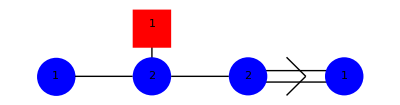
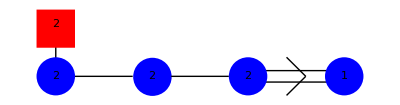
Orbit | dim(O) | dim(ℳ_H)^ℍ | d^t | Γ_1 | Γ_2 | Higgs HS | Character HWG | mHL HWG
{1^9} | 0 | 0 | {9} | -Graphics- | ... | 1 | 1 | ...
{2^2,1^5} | 12 | 6 | {7,2} | -Graphics- | -Graphics- | polynom/((1-t^2)^12) | 1/(1-t^2 m_2) | ...
{3,1^6} | 14 | 7 | {7,1^2} | -Graphics- | -Graphics- | polynom/((1-t^2)^14) | 1/((1-t^4 m_1^2) (1-t^2 m_2)) | ...
{2^4,1} | 16 | 8 | {5,4} | -Graphics- | ... | polynom/((1-t^2)^16) | 1/((1-t^2 m_2) (1-t^4 m_4^2)) | ...
{3,2^2,1^2} | 20 | 10 | {5,3,1} | -Graphics- | ... | polynom/((1-t^2)^20) | ... | ...
{3^2,1^3} | 22 | 11 | {5,2^2} | -Graphics- | ... | polynom/((1-t^2)^22) | ... | ...
{3^3} | 24 | 12 | {3^3} | -Graphics- | ... | polynom/((1-t^2)^24) | ... | ...
{5,1^4} | 24 | 12 | {5,1^4} | -Graphics- | ... | polynom/((1-t^2)^24) | ... | ...
{4^2,1} | 26 | 13 | {3,2^3} | -Graphics- | ... | polynom/((1-t^2)^26) | ... | ...
{5,2^2} | 26 | 13 | {3^2,1^3} | -Graphics- | ... | polynom/((1-t^2)^26) | ... | ...
{5,3,1} | 28 | 14 | {3,2^2,1^2} | -Graphics- | ... | polynom/((1-t^2)^28) | ... | ...
{7,1^2} | 30 | 15 | {3,1^6} | -Graphics- | ... | polynom/((1-t^2)^30) | ... | 1-t^8 h_1
{9} | 32 | 16 | {1^9} | -Graphics- | ... | polynom/((1-t^2)^30) | ... | 1Moduli Space Quivers for Nilpotent Orbits of B_4

```mathematica
Bseries[4]
```

```mathematica
(*For[n=1,n≤6, n++,
Print["n = ",n];
PrintBseriesModuli[n];
]*)
```

```mathematica
(*nmax=10;
TabView[Table[n->Bseries[n],{n,1,nmax}]]*)
```